# Parâmetros nu - fit 2024 ( Far Detector )

## T[1][2] (T_μτ) : Plots χ^2(var) - One variable only

## 2_Reducing a list of 2 variables to 1 : { Var, Var2, χ^2 } → { Var, χ^2 }

```mathematica
Red2for1[Inlist_, Var_, Var2_]:=
Module[{tab,lis,nunN,nun3,newlisOne,list,nun,nun2,newlis,NewlisOne},
(* Código da função *)
list=Inlist;

(* Creating the list: { Var, χ^2 } *)
nun={};nun2={};
tab=Table[{list[[i,Var]],list[[i,Var2]],list[[i,3]]},{i,Length@list}];
lis=tab[[Ordering@PadRight@tab]]; 
If[Var==1,
Do[
	If[ Length[nun]== 0,If[lis[[1,Var]]≠ lis[[i,Var]],AppendTo[nun,i]] ]
,{i,Length@lis}];
Do[
	If[ Length[nun2]== 0,If[lis[[1,Var2]]≠ lis[[i,Var2]],AppendTo[nun2,i]] ]
,{i,Length@lis}];
,
Do[
	If[ Length[nun]== 0,If[lis[[1,Var2]]≠ lis[[i,Var2]],AppendTo[nun,i]] ]
,{i,Length@lis}];
Do[
	If[ Length[nun2]== 0,If[lis[[1,Var]]≠ lis[[i,Var]],AppendTo[nun2,i]] ]
,{i,Length@lis}];
];
nunN=(nun-{1})/(nun2-{1});
nun2=nun2-{1};
nun3=(Length@lis)/(nunN*nun2);

newlisOne=Table[
{
 lis[[1+i*nunN[[1]],1]],
Min[ lis[[1+i*nunN[[1]]*nun2[[1]];;(1+i)*nunN[[1]],3]] ]
 }
,{i,0,nun3[[1]]-1}];


(* Return: *)
NewlisOne=newlisOne
]
```

## With BG : ϵ_μτ

### For ϵ_μτ:

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_02_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];

text = "DUNE_NSI_fit2D_WithBG_Eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list, 1, 2];
newlis
Export["/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/Table_DUNE_epsmut/Eps_pos.dat",newlis]

textPi = "DUNE_NSI_fit2D_WithBG_PiEps_alpha";
listPi=Import[StringJoin[pathImpor,textPi]];
newlisPi=Red2for1[listPi, 1, 2];
newlisPi
Export["/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/Table_DUNE_epsmut/Eps_min.dat",newlisPi]
```

{{0.,0.0000122289},{0.0005,0.00440679},{0.001,0.0220704},{0.0015,0.0610666},{0.002,0.131305},{0.0025,0.248387},{0.003,0.429128},{0.0035,0.690223},{0.004,1.04978},{0.0045,1.52702},{0.005,2.14211},{0.0055,2.91565},{0.006,3.86887},{0.0065,5.0231},{0.007,6.39986},{0.0075,8.02146},{0.008,9.90892},{0.0085,12.0836},{0.009,14.5669},{0.0095,17.3792},{0.01,20.5403}}

/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/Table_DUNE_epsmut/Eps_pos.dat

{{0.,0.0000122289},{0.0005,0.00270904},{0.001,0.00822666},{0.0015,0.0145284},{0.002,0.0215604},{0.0025,0.0311779},{0.003,0.0474519},{0.0035,0.076121},{0.004,0.124765},{0.0045,0.202237},{0.005,0.319323},{0.0055,0.488158},{0.006,0.727163},{0.0065,1.05228},{0.007,1.48124},{0.0075,2.0316},{0.008,2.7218},{0.0085,3.57004},{0.009,4.59659},{0.0095,5.82016},{0.01,7.26165}}

/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/Table_DUNE_epsmut/Eps_min.dat

0.0000122289

{{1}}

0.

0.0000122289

{{1}}

0.

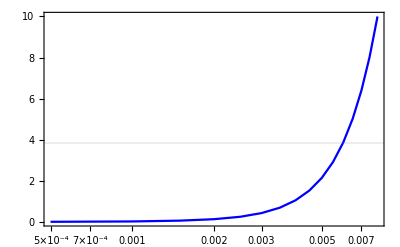

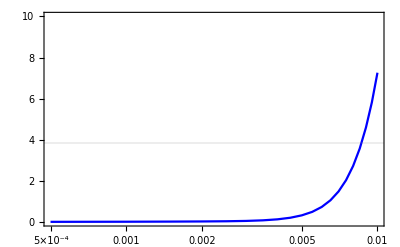

```mathematica
(* For ϵμτ positive *)
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];
min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]
(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListLogLinearPlot[DataMin, Joined->True, PlotStyle->Blue,PlotRange->{0,10},

PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}];


(* For ϵμτ negative *)
dataPi = newlisPi;
xPi=Transpose[dataPi][[1]];
chi2Pi= Transpose[dataPi][[2]];
minPi=Min[chi2Pi]
posPi = Position[chi2Pi,minPi]
xminPi=xPi[[posPi[[1,1]]]]
(* Data_Plot *)
DataMinPi=Table[{xPi[[i]],chi2Pi[[i]]-minPi},{i,1,Length[xPi]}];
PlotChi2NOPi=ListLogLinearPlot[DataMinPi, Joined->True, PlotStyle->Blue,
PlotRange->{0,10},

PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}];


(* With BG *)
plotWithoutBG=
Show[{PlotChi2NO},
ScalingFunctions->{"Log10",None},PlotRange->{0,10},
PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}]
plotWithoutBGPi=
Show[{PlotChi2NOPi},
ScalingFunctions->{"Log10",None},PlotRange->{0,10},
PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}]
```

### For α:

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_02_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];

text = "DUNE_NSI_fit2D_WithBG_Eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list, 2, 1];
newlis

textPi = "DUNE_NSI_fit2D_WithBG_PiEps_alpha";
listPi=Import[StringJoin[pathImpor,textPi]];
newlisPi=Red2for1[listPi, 2, 1];
newlisPi
```

{{-0.01,0.0179634},{-0.009,0.014822},{-0.008,0.0120947},{-0.007,0.00978111},{-0.006,0.00743934},{-0.005,0.00516975},{-0.004,0.00331336},{-0.003,0.00186979},{-0.002,0.000838655},{-0.001,0.000219593},{0.,0.0000122289},{0.001,0.000216192},{0.002,0.000831112},{0.003,0.00185662},{0.004,0.00329235},{0.005,0.00513792},{0.006,0.00739299},{0.007,0.0100572},{0.008,0.0131301},{0.009,0.0166114},{0.01,0.0205008}}

{{-0.01,0.0206571},{-0.009,0.016731},{-0.008,0.0132196},{-0.007,0.0101225},{-0.006,0.00743934},{-0.005,0.00516975},{-0.004,0.00331336},{-0.003,0.00186979},{-0.002,0.000838655},{-0.001,0.000219593},{0.,0.0000122289},{0.001,0.000216192},{0.002,0.000831112},{0.003,0.00185662},{0.004,0.00329235},{0.005,0.00513792},{0.006,0.00702722},{0.007,0.00912123},{0.008,0.0116245},{0.009,0.0145367},{0.01,0.0178574}}

0.0000122289

{{11}}

0.

0.0000122289

{{11}}

0.

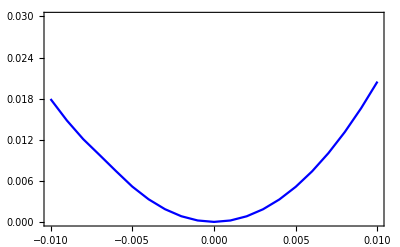

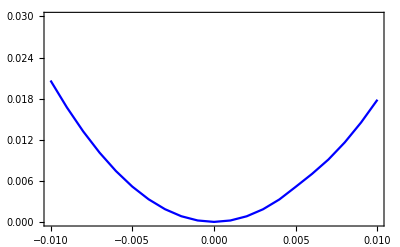

```mathematica
(* For ϵμτ positive *)
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];
min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]
(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Blue];


(* For ϵμτ negative *)
dataPi = newlisPi;
xPi=Transpose[dataPi][[1]];
chi2Pi= Transpose[dataPi][[2]];
minPi=Min[chi2Pi]
posPi = Position[chi2Pi,minPi]
xminPi=xPi[[posPi[[1,1]]]]
(* Data_Plot *)
DataMinPi=Table[{xPi[[i]],chi2Pi[[i]]-minPi},{i,1,Length[xPi]}];
PlotChi2NOPi=ListPlot[DataMinPi, Joined->True, PlotStyle->Blue];


(* With BG *)
plotWithoutBG=
Show[{PlotChi2NO},PlotRange->{0,0.03},Frame->True,GridLines->{{},{3.84}}]
plotWithoutBGPi=
Show[{PlotChi2NOPi},PlotRange->{0,0.03},Frame->True,GridLines->{{},{3.84}}]
```